## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGI";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy_r.csv";

mainFolder = "fit_PGI_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological,Q10];
```

Part::partw: Part 3 of {Null,Null} does not exist.

ToExpression::notstrbox: {{Null,Null}}⟦All,3⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Set::partw: Part 3 of {Null,Null} does not exist.

(g6p^c⇌f6p^c)^PGI

Null; Null

Structure: 2

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.37268 | 0.354046
0.391314 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | 0.001018 | 0.000876
0.00116 |  | M | 7.2 | 25 | mopskoh | 0.1 | 
1 | f6p | 0.000078 | 0.000069
0.000087 |  | M | 7.2 | 25 | mopskoh | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  | 
1 | f6p | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | pep | 0.00026 | 0.000247
0.000273 | f6p | 0.001 | Null | Null | M | 7.2 | 25 | mopskoh | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities={0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g6p^c⇌f6p^c)^PGI

Null; Null

Structure: 2

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.37268 | 0.354046
0.391314 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | 0.001018 | 0.000876
0.00116 |  | M | 7.2 | 25 | mopskoh | 0.1 | 
1 | f6p | 0.000078 | 0.000069
0.000087 |  | M | 7.2 | 25 | mopskoh | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  | 
1 | f6p | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGI[c] + g6p[c] <=> E_PGI[c]&g6p",
				"E_PGI[c]&g6p <=> E_PGI[c]&f6p",
				"E_PGI[c]&f6p <=> E_PGI[c] + f6p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGI^c)_^+g6p^c⇌(PGI^c&g6p^c)_^)^PGI1,((PGI^c&f6p^c)_^⇌(PGI^c)_^+f6p^c)^PGI2,((PGI^c&g6p^c)_^⇌(PGI^c&f6p^c)_^)^PGI3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGI^c)_^+g6p^c⇌(PGI^c&g6p^c)_^)^PGI1,Overscript[(PGI^c&f6p^c)_^⇌(PGI^c)_^+f6p^c, PGI2],((PGI^c&g6p^c)_^⇌(PGI^c&f6p^c)_^)^PGI3}
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

{((PGI^c)_^+g6p^c⇌(PGI^c&g6p^c)_^)^PGI1,((PGI^c&f6p^c)_^⇌(PGI^c)_^+f6p^c)^PGI2,((PGI^c&g6p^c)_^⇌(PGI^c&f6p^c)_^)^PGI3}

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGI^c&g6p^c)_^-((PGI^c&f6p^c)_^)/K_PGI3) Volume_c k_PGI3^⟶}

Volume_c (-(PGI^c&f6p^c)_^ k_PGI3^⟵+(PGI^c&g6p^c)_^ k_PGI3^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
flux = 0.0004910682765832838;
FluxExpression = absoluteFlux /. {metabolite["g6p", "c"] -> 0.0010544074634006885,metabolite["f6p","c"]-> 0,
     parameter["PGI_total"] -> 0.0000109144526868915, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "PGI"] /. FluxExpression;
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	f6p[c]	g6p[c]	param_PGI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt"	0.372679859
1	0	0.00010180000000000001	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.09090909090909091
1	0	0.00016134212699254143	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.13680688860321005
1	0	0.00025571003872767523	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.20076000891310172
1	0	0.00040527309962346035	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.2847472489508015
1	0	0.0006423145766808373	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.3868631798468572
1	0	0.0010180000000000002	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.5
1	0	0.0016134212699254144	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.6131368201531431
1	0	0.0025571003872767524	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.7152527510491985
1	0	0.0040527309962346035	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.7992399910868984
1	0	0.006423145766808372	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.8631931113967901
1	0	0.010180000000000002	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt"	0.9090909090909091
1	7.800000000000007e-6	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.09090909090909098
1	0.000012362166901196701	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.13680688860321016
1	0.000019592714165774757	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.200760008913102
1	0.000031052359303172786	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.28474724895080145
1	0.0000492146728694551	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.3868631798468571
1	0.00007800000000000007	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.5000000000000002
1	0.00012362166901196703	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.6131368201531434
1	0.00019592714165774758	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.7152527510491989
1	0.0003105235930317282	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.7992399910868984
1	0.0004921467286945509	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.86319311139679
1	0.0007800000000000007	0	1	7.2	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt"	0.9090909090909093
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt"	0.0004910682765832838

### Simulate data with uncertainty

```mathematica
Null
```

```mathematica
Null
```

### Parameter scan

```mathematica
Null
```

```mathematica
Null
```

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateFor_g6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/relRateRev_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.44164093242
best_fit: 1.44163645596
best_fit: 1.44163699795
best_fit: 1.44163612568
best_fit: 1.44163612664
best_fit: 1.4416399163
best_fit: 1.44163612787
best_fit: 1.44163623768
best_fit: 1.4416361304
best_fit: 1.44163617576

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_typeII/input/FBA2.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | haldaneRatio_1 | 0.00318652 | 0.0000101539 | 0.00272443 | 0.731037 | 0.37268 | 0.369955
1 | relRateFor_g6p | 0.328694 | 0.10804 | 0.102868 | 113.154 | 0.0909091 | 0.193777
1 | relRateFor_g6p | 0.304585 | 0.0927721 | 0.139056 | 101.644 | 0.136807 | 0.275863
1 | relRateFor_g6p | 0.273078 | 0.0745717 | 0.175732 | 87.5332 | 0.20076 | 0.376492
1 | relRateFor_g6p | 0.234895 | 0.0551759 | 0.204305 | 71.7495 | 0.284747 | 0.489052
1 | relRateFor_g6p | 0.192583 | 0.0370882 | 0.215891 | 55.8056 | 0.386863 | 0.602754
1 | relRateFor_g6p | 0.150066 | 0.0225198 | 0.206376 | 41.2752 | 0.5 | 0.706376
1 | relRateFor_g6p | 0.111343 | 0.0123972 | 0.179182 | 29.2239 | 0.613137 | 0.792319
1 | relRateFor_g6p | 0.0791292 | 0.00626144 | 0.142948 | 19.9856 | 0.715253 | 0.858201
1 | relRateFor_g6p | 0.0543159 | 0.00295022 | 0.106478 | 13.3224 | 0.79924 | 0.905718
1 | relRateFor_g6p | 0.0363289 | 0.00131979 | 0.0753124 | 8.72486 | 0.863193 | 0.938506
1 | relRateFor_g6p | 0.0238642 | 0.0005695 | 0.0513519 | 5.64871 | 0.909091 | 0.960443
1 | relRateRev_f6p | 0.00869199 | 0.0000755507 | 0.00180137 | 1.98151 | 0.0909091 | 0.0891077
1 | relRateRev_f6p | 0.00825558 | 0.0000681546 | 0.00257603 | 1.88296 | 0.136807 | 0.134231
1 | relRateRev_f6p | 0.00764677 | 0.000058473 | 0.00350391 | 1.74532 | 0.20076 | 0.197256
1 | relRateRev_f6p | 0.00684593 | 0.0000468668 | 0.00445338 | 1.56398 | 0.284747 | 0.280294
1 | relRateRev_f6p | 0.00587025 | 0.0000344598 | 0.00519395 | 1.34258 | 0.386863 | 0.381669
1 | relRateRev_f6p | 0.0047867 | 0.0000229125 | 0.00548063 | 1.09613 | 0.5 | 0.494519
1 | relRateRev_f6p | 0.00370043 | 0.0000136932 | 0.00520208 | 0.848436 | 0.613137 | 0.607935
1 | relRateRev_f6p | 0.00271765 | 7.3856×10^-6 | 0.0044618 | 0.623807 | 0.715253 | 0.710791
1 | relRateRev_f6p | 0.00190766 | 3.63918×10^-6 | 0.00350301 | 0.438293 | 0.79924 | 0.795737
1 | relRateRev_f6p | 0.00128988 | 1.66379×10^-6 | 0.00255993 | 0.296565 | 0.863193 | 0.860633
1 | relRateRev_f6p | 0.000845965 | 7.15657×10^-7 | 0.0017691 | 0.194601 | 0.909091 | 0.907322
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateFor | 0.290247 | 0.0842432 | 28.5553 | 95.0953 | 30.0281 | 58.5834
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
1 | absRateRev | 0.00319846 | 0.0000102302 | 0.220337 | 0.733768 | 30.0281 | 29.8078
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292
3 | customRatio_1 | 0.031899 | 0.00101755 | 0.0000347762 | 7.08175 | 0.000491068 | 0.000456292

### Simulated Data and Best Fit Data Plot

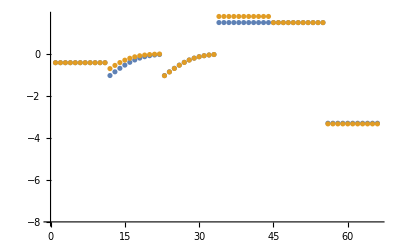

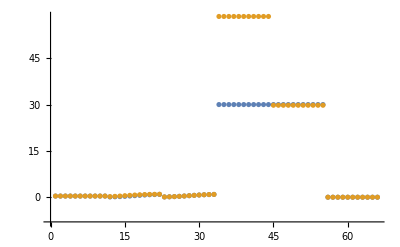

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

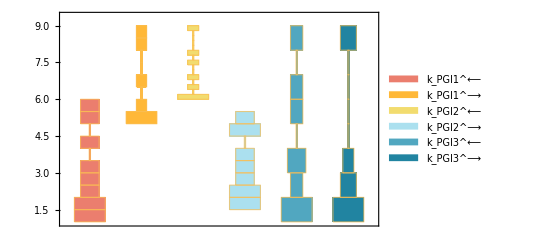

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

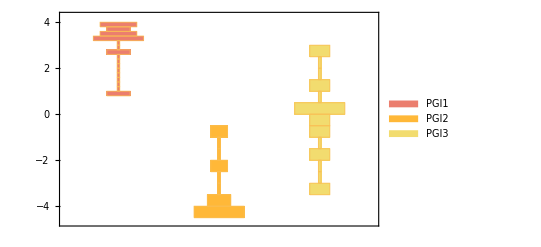

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

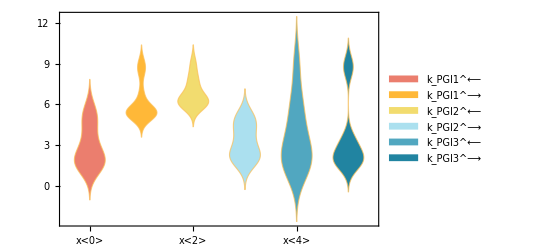

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

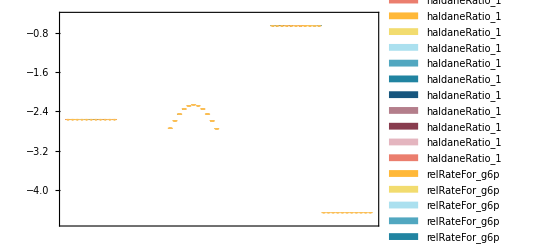

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.001018 | 0.000423411 | 58.4076
0.000078 | 0.0000797288 | 2.21637

```mathematica
assumedSaturatingConc
```

1

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
30.0281 | 58.5834 | 95.0953
30.0281 | 29.8078 | 0.733768

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.37268 | 0.369955 | 0.731037

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.37268 | 0.369955 | 0.731037

```mathematica
print[inhibitionList]
```

print[{}]

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

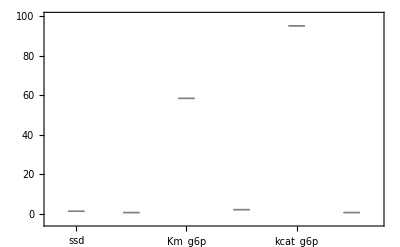

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

```mathematica
{eqnNameList,eqnValList,eqnValListPy,fileList,fileListSub}=exportRateEqs[inputPath,absoluteRateForward,absoluteRateReverse,relativeRateForward,relativeRateReverse,metsSub,metSatForSub,metSatRevSub,rateConstsSub,otherAbsoluteRatesForward,otherAbsoluteRatesReverse];
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 7;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/pgi already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgi\rateconst_labels_pgi.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgi\S_pgi.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PGI[c],E_PGI[c]&f6p,f6p[c],g6p[c],E_PGI[c]&g6p}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgi\species_pgi.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PGI1: E_PGI[c] + g6p[c] <=> E_PGI[c]&g6p,PGI2: E_PGI[c]&f6p <=> E_PGI[c] + f6p[c],PGI3: E_PGI[c]&g6p <=> E_PGI[c]&f6p}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgi\reactions_pgi.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PGI[c],E_PGI[c]&f6p,E_PGI[c]&g6p}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PGI1_rev*k_PGI2_fwd*param_PGI_total) - k_PGI2_fwd*k_PGI3_fwd*param_PGI_total - k_PGI1_rev*k_PGI3_rev*param_PGI_total)/(g6p(c)*k_PGI1_fwd*k_PGI2_fwd + k_PGI1_rev*k_PGI2_fwd + f6p(c)*k_PGI1_rev*k_PGI2_rev + g6p(c)*k_PGI1_fwd*k_PGI3_fwd + k_PGI2_fwd*k_PGI3_fwd + f6p(c)*k_PGI2_rev*k_PGI3_fwd + g6p(c)*k_PGI1_fwd*k_PGI3_rev + k_PGI1_rev*k_PGI3_rev + f6p(c)*k_PGI2_rev*k_PGI3_rev))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgi\rateconst_clusters_pgi.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgi\rateLaw_pgi.txt